# Caos en un atractor extraño

## Ecuaciones de Lorenz

```mathematica
r=28;
s=10;
b=8/3;
```

```mathematica
sol1=NDSolve[{x'[t]==s*(y[t]-x[t]),y'[t]==x[t]*(r-z[t])-y[t],z'[t]==x[t]*y[t]-b*z[t],x[0]==0,y[0]==1/100,z[0]==0},{x,y,z},{t,0,1000}];
```

Vemos que las soluciones oscilan pero no son periódicas ni cuasiperiódicas

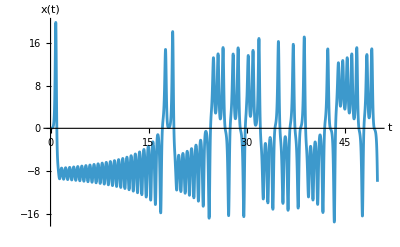

```mathematica
Plot[Evaluate[x[t]/.sol1],{t,0,50},PlotRange->All,AxesLabel->{t,x[t]},PlotPoints->100,MaxRecursion->10]
```

Las soluciones son atraídas por un atractor “extraño”:

```mathematica
ParametricPlot3D[{x[t],y[t],z[t]}/.sol1,{t,0,100},AxesLabel->{x,y,z},MaxRecursion->10,PlotPoints->100,PlotStyle->Thick,ColorFunction->Function[{x,y,z,t},ColorData["TemperatureMap"][t]]]
```

-Graphics3D-

Comparamos con otra solución con casi las mismas condiciones iniciales:

```mathematica
sol2=NDSolve[{x'[t]==s*(y[t]-x[t]),y'[t]==x[t]*(r-z[t])-y[t],z'[t]==x[t]*y[t]-b*z[t],x[0]==0+1/1000,y[0]==1/100,z[0]==0},{x,y,z},{t,0,1000}];
```

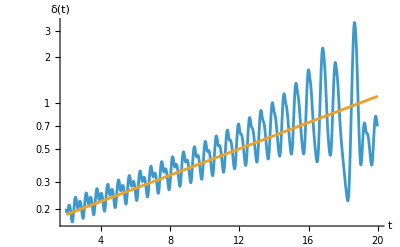

```mathematica
LogPlot[{Norm[Evaluate[{x[t],y[t],z[t]}/.sol1]-Evaluate[{x[t],y[t],z[t]}/.sol2]],0.15*Exp[0.1*t]},{t,2,20},AxesLabel->{t,δ[t]}]
```